# Feeding on n-prey-at-a-time Type II functional response

## Preamble

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
SetDirectory["../figs/"]
```

/Users/marknovak/Git/FR_n-prey-at-a-time/figs

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
Clear[n];
```

## Functional response

#### Partial summation

```mathematica
s=Sum[x^i,{i,1,n}]
(s/(1+s))//Simplify
```

(x (-1+x^n))/(-1+x)

(x (-1+x^n))/(-1+x^(1+n))

#### Infinite summation

```mathematica
s=Sum[x^i,{i,1,∞}]
(s/(1+s))//Simplify
```

-x/(-1+x)

x

### Feeding on n prey at a time - Functional response

Now  substitute  ' x -> a h R' to get ...

```mathematica
S[n_]=Sum[(a h R )^i,{i,1,n}]
fracF[n_,R_]=(S[n]/(1+S[n]))//Simplify
f[n_,R_]=(1/h)fracF[n,R]//FullSimplify
```

(a h R (-1+(a h R)^n))/(-1+a h R)

(a h R (-1+(a h R)^n))/(-1+(a h R)^(1+n))

(a R (-1+(a h R)^n))/(-1+(a h R)^(1+n))

```mathematica
f[1,R]//Simplify
f[2,R]//Simplify
f[3,R]//Factor
f[0.5,R]
f[1.5,R]
```

(a R)/(1+a h R)

(a R (1+a h R))/(1+a h R+a^2 h^2 R^2)

(a R (1+a h R+a^2 h^2 R^2))/((1+a h R) (1+a^2 h^2 R^2))

(a R (-1+(a h R)^0.5))/(-1+(a h R)^1.5)

(a R (-1+(a h R)^1.5))/(-1+(a h R)^2.5)

Fraction handling i prey specifically

```mathematica
fracFn[i_,n_,R_]=((a h R)^i/(1+S[n]))//Simplify
```

((a h R)^i (-1+a h R))/(-1+(a h R)^(1+n))

```mathematica
fracFn[1,2,R]//Simplify
```

(a h R)/(1+a h R+a^2 h^2 R^2)

Infinite summation gives the “Type 1” functional response

```mathematica
Sinf[n_]=Sum[(a h R)^i,{i,1,∞}];
finf[R_]=(1/h)(Sinf[n]/(1+Sinf[n]));
finf[R]//Simplify
```

a R

#### Illustrate multiple-prey functional response

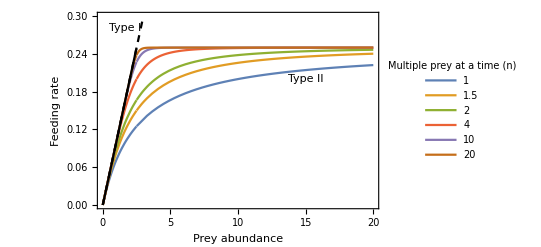

```mathematica
Clear[fparms]
Clear[nvals]
fparms={h-> 4,a-> 0.1};
nvals={1,1.5,2, 4, 10, 20};
prange = {{0,20},{0,0.3}};
p1=Plot[Evaluate[f[n,R]/.fparms/.n-> nvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[nvals,
LegendLabel-> "Multiple prey at a time (n)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]},
Epilog-> Text["Type II",{15,0.2}]
];
p2a=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black,Dashed},
PlotLabels-> Placed[{"Type I"},{1.7,0.27},Background-> None]];
p2b=Plot[finf[R]/.fparms,{R,0,1/(a h)/.fparms},
PlotRange->prange,
PlotStyle->{Black}];
P1=Show[p1,p2a,p2b]
Export["FR_n-prey-at-a-time.pdf",P1,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Fraction of predator population handling exactly i of n-max prey

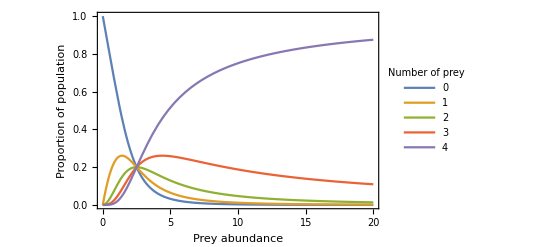

```mathematica
nmax=4;
prange = {{0,20},{0,1}};
P8=Plot[{1-fracF[nmax,R]/.fparms,Evaluate[Table[fracFn[i,nmax,R]/.fparms,{i,1,nmax}]]},{R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[Range[0,nmax],
LegendLabel-> "Number of prey" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Center}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Proportion of population",14]}]
Export["FR_n-prey-at-a-time_fracF.pdf",P8,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

Prey abundance where predator proportions are all equal

```mathematica
fracFn[1,n,R]
fracFn[2,n,R]
```

(a h R (-1+a h R))/(-1+(a h R)^(1+n))

(a^2 h^2 R^2 (-1+a h R))/(-1+(a h R)^(1+n))

```mathematica
Solve[fracFn[1,nmax,R]==fracFn[2,nmax,R],R]
```

{{R→0},{R→1/(a h)}}

#### Compare to diminishing handling times

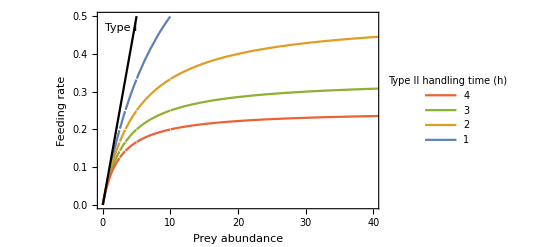

```mathematica
hvals = Table[h,{h,1,4,1}];

prange = {{0,40},{0,0.5}};
p3=Plot[Evaluate[f[1,R]/.Drop[fparms,1]/.h-> hvals], {R,0,100},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[hvals,
LegendLabel-> "Type II handling time (h)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"ReversedRow",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]}
];
p2=Plot[finf[R]/.fparms,{R,0,100},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},{2.8,0.45},Background-> None]];
P2=Show[p3,p2]
Export["FR_htime-to-zero.pdf",P2,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Density-dependent diminishing handling time (exponential decay)

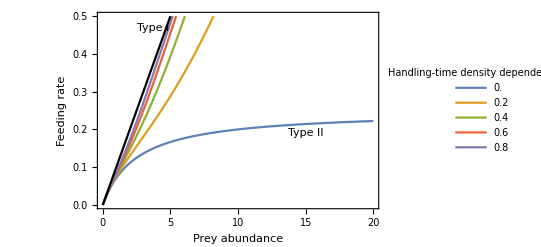

```mathematica
fT2h[R_]=(a R)/(1 + a h Exp[-(η R)] R);
ηvals = Table[η,{η,0,0.8,0.2}];

prange = {{0,20},{0,0.5}};
p4=Plot[Evaluate[fT2h[R]/.fparms/.η->ηvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[ηvals,
LegendLabel-> "Handling-time density dependence (η)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]},
Epilog-> Text["Type II",{15,0.19}]
];
p2=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},{{2.5,0.45},{0,0}}],Background->Transparent];
P3=Show[p4,p2]
Export["FR_htime_diminishing.pdf",P3,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Density-dependent diminishing handling time (adaptively-optimal prey; Okuyama 2010)

```mathematica
fT2h2[R_]=(a R)/(1 + a (√(a R Θ))/(a R) R)//Simplify;
Θvals = Table[Θ,{Θ,2,8,2}];
```

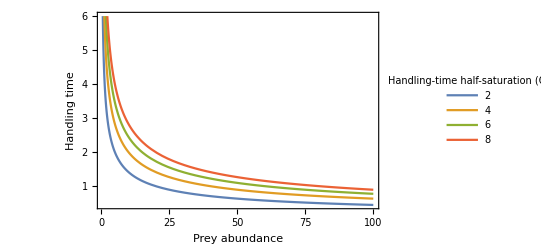

```mathematica
Plot[Evaluate[Table[(√(a R Θ))/(a R)/.fparms,{Θ,2,8,2}]], {R,0,100},
PlotRange->{{0,All},{0,6}},
PlotLegends -> Placed[
LineLegend[Θvals,
LegendLabel-> "Handling-time half-saturation (Θ)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Top}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Handling time",14]}]
```

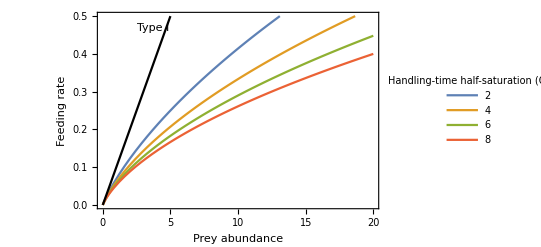

```mathematica
prange = {{0,20},{0,0.5}};
p4b=Plot[Evaluate[fT2h2[R]/.fparms/.Θ->Θvals], {R,0,20},
PlotRange->prange,
PlotLegends -> Placed[
LineLegend[Θvals,
LegendLabel-> "Handling-time half-saturation (Θ)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->1,
LegendLayout-> {"Row",1},
Spacings->0.15],
{Right,Bottom}],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{
Style["Prey abundance",14],
Style["Feeding rate",14]}
];
p2b=Plot[finf[R]/.fparms,{R,0,20},
PlotRange->prange,
PlotStyle->{Black},
PlotLabels-> Placed[{"Type I"},{{2.5,0.45},{0,0}}],Background->Transparent];
P3b=Show[p4b,p2b]
Export["FR_htime_diminishing-opt.pdf",P3b,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

## Incorporate into Rosenzweig-MacArthur model

```mathematica
Clear[dRdt,dPdt]
dRdt=r R (1-R/Κ)-f[n,R]P;
dPdt=e f[n,R]P-d P;

Clear[nvals]
nvals={1,2, 4, 10, 20};

(*Good isocline spacing over dynamical range*)
(* parms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2} *)
parms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2};

model[n_]:={
R'[t]==r R[t](1-R[t]/Κ)-(a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t],
R[0]==0.1,
P'[t]==e (a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t]-d P[t],
P[0]==0.1
};
```

## Isocline analysis

#### Prey isocline

```mathematica
isoR[R_]=P/.Solve[dRdt==0,P]//FullSimplify
```

{(r (-1+(a h R)^(1+n)) (-R+Κ))/(a (-1+(a h R)^n) Κ)}

Compare to Type I and Type II

```mathematica
P/.Solve[(dRdt/.{h-> 0, n-> 1})==0,P]//FullSimplify
P/.Solve[(dRdt/.{h-> h, n-> 1})==0,P]//FullSimplify
```

{(r (-R+Κ))/(a Κ)}

{-(r (1+a h R) (R-Κ))/(a Κ)}

#### Predator isocline

Type I and Type II

```mathematica
R/.Solve[(dPdt/.h-> 0)==0,R]//TableForm
R/.Solve[(dPdt/.{h-> 0,n-> 1})==0,R]//TableForm

R/.Solve[(dPdt/.n->1)==0,R]//TableForm
```

((-1+0^(1+n)) d)/((-1+0^n) a e)

d/(a e)

d/(a (e-d h))

Solving multi-prey system for isoP gives n solutions for n-prey-at-a-time (all but one of which are complex), so gets complicated quickly.  But isoP always remains independent of R or P.  Thus evaluate numerically and remove complex and negative values. The real (non-complex) solution also converges on the solution of the Type I functional response (shown numerically below), as would be expected as h -> 0.

```mathematica
R/.Solve[(dPdt/.n->2)==0,R]//FullSimplify//TableForm
R/.Solve[(dPdt/.n->3)==0,R]//FullSimplify//TableForm
```

(2 d)/(a (e-d h)+√(a^2 (e-d h) (e+3 d h)))
(a (e-d h)+√(a^2 (e-d h) (e+3 d h)))/(2 a^2 h (-e+d h))

(4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)-(2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))/(6 a^3 h^2 (-e+d h) (a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3))
(-8 (-2)^(1/3) a^4 h^2 (e-d h)^2-4 a^2 h (-e+d h) (a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(1-ⅈ √3) (2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))/(12 a^3 h^2 (-e+d h) (a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3))
(4 ⅈ 2^(1/3) (ⅈ+√3) a^4 h^2 (e-d h)^2-4 a^2 h (-e+d h) (a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(1+ⅈ √3) (2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))/(12 a^3 h^2 (-e+d h) (a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3))

#### Visualize

```mathematica
Clear[isoP]
isoP[ν_]:=Re[Select[R/.Solve[(dPdt/.n->ν)==0,R]/.parms,Abs[Im[#]]< 10^-13&&Re[#]>0&]]//Flatten
```

Values of predator isocline converge on constant very quickly

```mathematica
isoPvals=isoP/@nvals//Flatten
```

{44.4444,23.1,17.5223,16.0697,16.0008}

```mathematica
addEpilog[g_Graphics,epi_List]:=With[{styles=Cases[g[[1]],{dir__,__Line}:>Directive[dir],-5]},Show[g,Epilog->{styles,epi}~Flatten~{2}]]

p4=Plot[Evaluate[isoR[R]/.parms/.n-> nvals],{R,0,100},
PlotRange->{{0,1+Κ/.parms},{0,50}},
PlotRangePadding->0,
AspectRatio->0.8,
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey abundance",14],
Style["Predator abundance",14]}
];

p5a=Legended[
addEpilog[p4,InfiniteLine[{{#,0},{#,1}}]&/@isoPvals],
Placed[
LineLegend[
ColorData[97,"ColorList"][[1;;Length[nvals]]],
nvals,
LegendLabel-> "n prey at a time" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings-> 0.1],
{{0.7,0.57},{0,0}}]];
```

```mathematica
isoRvals=MapThread[ReplaceAll,{isoR[isoPvals]/.parms//Flatten,Thread[n->#]&/@nvals}];
pts=Transpose[{isoPvals,isoRvals}];
p5d=Graphics[Prepend[Riffle[ColorData[97,"ColorList"][[1;;Length[nvals]]],Point/@pts],PointSize[.02]]];
```

#### Add Isocline for linear Type I

```mathematica
dRdtinf=r R (1-R/Κ)-a R P;
dPdtinf=e a R P-d P;
isoRinf[R_]=P/.Solve[dRdtinf==0,P]
isoPinf=R/.Solve[dPdtinf==0,R]
```

{-(r (R-Κ))/(a Κ)}

{d/(a e)}

As n -> ∞ the many - prey prey isocline breaks away from the type - I prey isocline at R = 1/ (a h) . 
   [Obtained by solving ' a R = 1 / h' for R .]

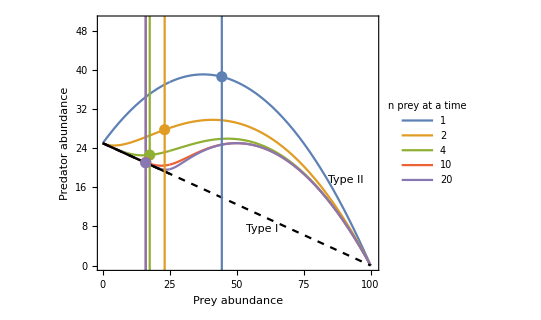

```mathematica
p5b=Plot[Evaluate[isoRinf[R]/.parms],{R,0,100},
PlotLabels->Placed[{"Type I","Type II"},{{60,9},{90,16}},Background->Transparent],
PlotStyle->{Black,Dashed},
GridLines->{isoPinf/.parms,None},
GridLinesStyle->Directive[Thickness[0.003],Black]];
p5c=Plot[Evaluate[isoRinf[R]/.parms],{R,0,1/(a h)/.parms},
PlotStyle->Black];

(* p5d=Graphics[{PointSize[0.015],Point[{(isoPinf/.parms)[[1]],(isoRinf[isoPinf][[1]]/.parms)[[1]]}]}]; *)

P4=Show[p5a,p5b,p5c,p5d]
Export["Isoclines.pdf",P4,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

### Prey isocline as a function of handling time

```mathematica
hvals2={0.5,1,2,3,4};
```

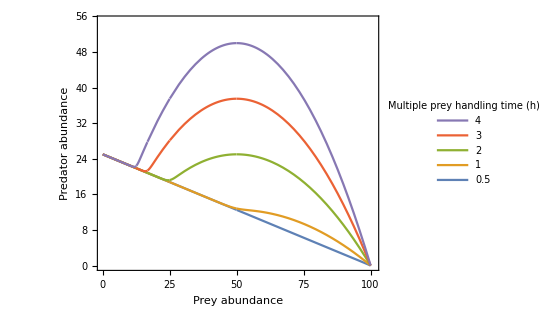

```mathematica
Plot[Evaluate[isoR[R]/.Drop[parms,-1]/.n-> 40/.h-> hvals2],{R,0,100},
PlotRange->{{0,1+Κ/.parms},{0,55}},
PlotRangePadding->0,
AspectRatio->0.8,
PlotLegends -> Placed[
LineLegend[hvals2,
LegendLabel-> "Multiple prey handling time (h)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"ReversedRow",1},
Spacings->0.15],
{Left,Bottom}],
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey abundance",14],
Style["Predator abundance",14]}]
```

#### Compare to Type II

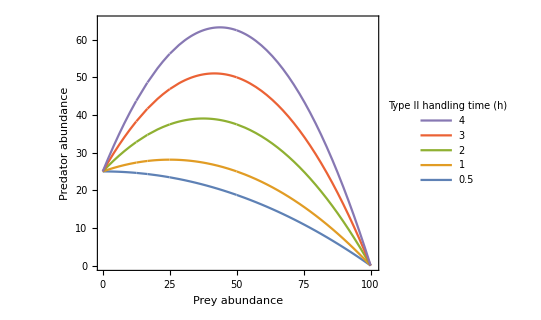

```mathematica
Plot[Evaluate[isoR[R]/.Drop[parms,-1]/.n-> 1/.h-> hvals2],{R,0,100},
PlotRange->{{0,1+Κ/.parms},{0,65}},
PlotRangePadding->0,
AspectRatio->0.8,
PlotLegends -> Placed[
LineLegend[hvals2,
LegendLabel-> "Type II handling time (h)" ,
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
LegendLayout-> {"ReversedRow",1},
Spacings->0.15],
{Left,Bottom}],
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey abundance",14],
Style["Predator abundance",14]}]
```

## Analytics

```mathematica
A=JacobianMatrix[{dRdt,dPdt},{R,P}]//FullSimplify;
MatrixForm@A
```

(r+(a P (-1+(a h R)^n (1+n-a h n R)))/((-1+(a h R)^(1+n))^2)-(2 r R)/Κ | -(a R (-1+(a h R)^n))/(-1+(a h R)^(1+n))
(a e P (1+(a h R)^n (-1+n (-1+a h R))))/((-1+(a h R)^(1+n))^2) | -d+(a e R (-1+(a h R)^n))/(-1+(a h R)^(1+n)))

Solving for equilbria symbolically for general ‘n’ is not possible , but solving for n < 3 works and results in ‘n’ potential  coexistence equilibria of which only one is feasible and real-valued.  It tends to be the 2nd equilibrium that is the feasible coexistence equilibrium.
Note that, when evaluated at the feasible coexistence steady state,  the [2, 2] element (predator effect on predator) of the Jacobian is always zero (regardless of n).  Thus the trace is determined entirely by the prey’s self-effect.
The [1,2] element (predator effect on prey) is always -d/e.

```mathematica
pickSS=2;
Clear[n]
```

#### n = 1

```mathematica
n=1;
equil=Solve[{dRdt==0,dPdt==0},{R,P}];
equil//TableForm
equil/.parms//TableForm

Aeq=A/.equil[[pickSS]]//Simplify;
MatrixForm@Aeq

Det[Aeq]//Simplify
Tr[Aeq]//Simplify

Det0=Solve[Det[Aeq]==0, d]
Tr0=Solve[Tr[Aeq]==0, d]
```

R→0 | P→0
R→d/(a (e-d h)) | P→(e r (-d+a e Κ-a d h Κ))/(a^2 (e-d h)^2 Κ)
R→Κ | P→0

R→0 | P→0
R→44.4444 | P→38.5802
R→100 | P→0

(-(d r (e-a e h Κ+d h (1+a h Κ)))/(a e (e-d h) Κ) | -d/e
r (e-d h-d/(a Κ)) | 0)

-(d r (d-a e Κ+a d h Κ))/(a e Κ)

-(d r (e-a e h Κ+d h (1+a h Κ)))/(a e (e-d h) Κ)

{{d→0},{d→(a e Κ)/(1+a h Κ)}}

{{d→0},{d→(-e+a e h Κ)/(h (1+a h Κ))}}

#### n = 2

```mathematica
n=2;
equil=Solve[{dRdt==0,dPdt==0},{R,P}];
equil//TableForm
equil/.parms//TableForm

Aeq=A/.equil[[pickSS]]//Simplify;
MatrixForm@Aeq

Det[Aeq]//Simplify
Tr[Aeq]//Simplify

Det0=Solve[Det[Aeq]==0, d]
(* Tr0=Solve[Tr[Aeq]==0, d] *)
```

R→0 | P→0
R→(a e-a d h-√(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2))/(2 (-a^2 e h+a^2 d h^2)) | P→(d e r-(a^2 e^3 r)/(2 (-a^2 e h+a^2 d h^2))+(a^2 d e^2 h r)/(-a^2 e h+a^2 d h^2)-(a^2 d^2 e h^2 r)/(2 (-a^2 e h+a^2 d h^2))+(a e^2 √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r)/(2 (-a^2 e h+a^2 d h^2))-(a d e h √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r)/(2 (-a^2 e h+a^2 d h^2))-(a^3 e^3 h r Κ)/(2 (-a^2 e h+a^2 d h^2))+(a^3 d e^2 h^2 r Κ)/(-a^2 e h+a^2 d h^2)-(a^3 d^2 e h^3 r Κ)/(2 (-a^2 e h+a^2 d h^2))+(a^2 e^2 h √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r Κ)/(2 (-a^2 e h+a^2 d h^2))-(a^2 d e h^2 √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r Κ)/(2 (-a^2 e h+a^2 d h^2)))/(-a^2 d e h Κ+a^2 d^2 h^2 Κ)
R→(a e-a d h+√(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2))/(2 (-a^2 e h+a^2 d h^2)) | P→(d e r-(a^2 e^3 r)/(2 (-a^2 e h+a^2 d h^2))+(a^2 d e^2 h r)/(-a^2 e h+a^2 d h^2)-(a^2 d^2 e h^2 r)/(2 (-a^2 e h+a^2 d h^2))-(a e^2 √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r)/(2 (-a^2 e h+a^2 d h^2))+(a d e h √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r)/(2 (-a^2 e h+a^2 d h^2))-(a^3 e^3 h r Κ)/(2 (-a^2 e h+a^2 d h^2))+(a^3 d e^2 h^2 r Κ)/(-a^2 e h+a^2 d h^2)-(a^3 d^2 e h^3 r Κ)/(2 (-a^2 e h+a^2 d h^2))-(a^2 e^2 h √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r Κ)/(2 (-a^2 e h+a^2 d h^2))+(a^2 d e h^2 √(a^2 e^2+2 a^2 d e h-3 a^2 d^2 h^2) r Κ)/(2 (-a^2 e h+a^2 d h^2)))/(-a^2 d e h Κ+a^2 d^2 h^2 Κ)
R→Κ | P→0

R→0 | P→0
R→23.1 | P→27.7561
R→-48.1 | P→-111.306
R→100 | P→0

(-(r (√(a^2 (e^2+2 d e h-3 d^2 h^2)) (e^2-2 d e h-d^2 h^2)+a^2 h (-e^3+d e^2 h+3 d^2 e h^2-3 d^3 h^3) Κ-a (e-d h) (e^2-e h √(a^2 (e^2+2 d e h-3 d^2 h^2)) Κ+d h^2 (-3 d+√(a^2 (e^2+2 d e h-3 d^2 h^2)) Κ))))/(2 a^2 d e h^2 (-e+d h) Κ) | -d/e
(√(a^2 (e^2+2 d e h-3 d^2 h^2)) r (√(a^2 (e^2+2 d e h-3 d^2 h^2))+a^2 h (-e+d h) Κ-a (e+h (d-√(a^2 (e^2+2 d e h-3 d^2 h^2)) Κ))))/(2 a^3 d h^2 Κ) | 0)

(r (-((e+d h) √(a^2 (e^2+2 d e h-3 d^2 h^2)))+a^2 h (e^2+2 d e h-3 d^2 h^2) Κ+a (e-d h) (e+3 d h-h √(a^2 (e^2+2 d e h-3 d^2 h^2)) Κ)))/(2 a^2 e h^2 Κ)

-1/(2 a^2 d e h^2 (-e+d h) Κ)r (√(a^2 (e^2+2 d e h-3 d^2 h^2)) (e^2-2 d e h-d^2 h^2)+a^2 h (-e^3+d e^2 h+3 d^2 e h^2-3 d^3 h^3) Κ-a (e-d h) (e^2-e h √(a^2 (e^2+2 d e h-3 d^2 h^2)) Κ+d h^2 (-3 d+√(a^2 (e^2+2 d e h-3 d^2 h^2)) Κ)))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{d→0},{d→-e/(3 h)},{d→e/h},{d→(a e Κ (1+a h Κ))/(1+a h Κ+a^2 h^2 Κ^2)}}

#### n = 3

```mathematica
n=3;
equil=Solve[{dRdt==0,dPdt==0},{R,P}]//Simplify;
equil//TableForm
equil/.parms//TableForm

Aeq=A/.equil[[pickSS]]//Simplify;
MatrixForm@Aeq

Det[Aeq]//Simplify
Tr[Aeq]//Simplify

(* Det0=Solve[Det[Aeq]==0, d] *)
(* Tr0=Solve[Tr[Aeq]==0, d] *)
```

R→0 | P→0
R→(-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))/(6 a^3 h^2 (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)) | P→(e r (2 2^(2/3) a^8 h^4 (e-d h)^3 (e+8 d h)+2 2^(2/3) √3 a^2 h (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2))+2 a^4 h^2 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)+a^6 h^3 (e-d h)^2 (5 e+4 d h) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)-√3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+2^(2/3) a^9 h^5 (e-d h)^3 (7 e+20 d h) Κ+3 2^(2/3) √3 a^3 h^2 (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) Κ-2 a^5 h^3 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ+4 a^7 h^4 (e-d h)^3 (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ))/(6 a^6 d h^4 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ)
R→(4 2^(1/3) (1+ⅈ √3) a^4 h^2 (e-d h)^2-4 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+ⅈ (ⅈ+√3) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))/(12 a^3 h^2 (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)) | P→(e (4 2^(1/3) (-ⅈ+√3) a^4 h^2 (e-d h)^2+4 ⅈ a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(ⅈ+√3) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) r (4 2^(1/3) (-ⅈ+√3) a^4 h^2 (e-d h)^2+4 ⅈ a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(ⅈ+√3) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)+12 ⅈ a^3 h^2 (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ))/(144 a^6 d h^4 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ)
R→(4 2^(1/3) (1-ⅈ √3) a^4 h^2 (e-d h)^2-4 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)-ⅈ (-ⅈ+√3) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))/(12 a^3 h^2 (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)) | P→(e (4 2^(1/3) (ⅈ+√3) a^4 h^2 (e-d h)^2-4 ⅈ a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-ⅈ+√3) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) r (4 2^(1/3) (ⅈ+√3) a^4 h^2 (e-d h)^2-4 ⅈ a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-ⅈ+√3) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)-12 ⅈ a^3 h^2 (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ))/(144 a^6 d h^4 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ)
R→Κ | P→0

R→0 | P→0
R→19.0071 | P→24.0537
R→-22.0035-31.2616 ⅈ | P→-26.6753-70.3421 ⅈ
R→-22.0035+31.2616 ⅈ | P→-26.6753+70.3421 ⅈ
R→100 | P→0

(r-((-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) r)/(3 a^3 h^2 (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ)+(6 (e-d h)^2 (-1-((-4 2^(1/3) a^4 h^2 (e-d h)^2-10 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) (-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))^3)/(432 a^8 h^4 (e-d h)^4 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(4/3))) r (2 2^(2/3) a^8 h^4 (e-d h)^3 (e+8 d h)+2 2^(2/3) √3 a^2 h (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2))+2 a^4 h^2 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)+a^6 h^3 (e-d h)^2 (5 e+4 d h) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)-√3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+2^(2/3) a^9 h^5 (e-d h)^3 (7 e+20 d h) Κ+3 2^(2/3) √3 a^3 h^2 (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) Κ-2 a^5 h^3 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ+4 a^7 h^4 (e-d h)^3 (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ))/(a d e h^2 (-4 2^(1/3) a^4 h^2 (e-d h)^2-8 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))^2 Κ) | -((-e+d h) (-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) (-1+((-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))^3)/(216 a^6 h^3 (-e+d h)^3 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2))))))/(e h (4 2^(1/3) a^4 h^2 (e-d h)^2+8 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)-(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)))
-((8 2^(2/3) a^8 h^4 (e-d h)^4-4 a^4 h^2 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)-a^6 h^3 (e-d h)^2 (7 e+20 d h) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)) r (2 2^(2/3) a^8 h^4 (-e+d h)^3 (e+8 d h)-2 2^(2/3) √3 a^2 h (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2))-2 a^4 h^2 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)-a^6 h^3 (e-d h)^2 (5 e+4 d h) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+√3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+2^(2/3) a^9 h^5 (-e+d h)^3 (7 e+20 d h) Κ-3 2^(2/3) √3 a^3 h^2 (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) Κ+2 a^5 h^3 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ-4 a^7 h^4 (e-d h)^3 (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ))/(36 a^9 d h^6 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(4/3) Κ) | 0)

-(((-e+d h) (8 2^(2/3) a^8 h^4 (e-d h)^4-4 a^4 h^2 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)-a^6 h^3 (e-d h)^2 (7 e+20 d h) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)) (-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) (-1+(-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))^3/(216 a^6 h^3 (-e+d h)^3 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2))))) r (2 2^(2/3) a^8 h^4 (-e+d h)^3 (e+8 d h)-2 2^(2/3) √3 a^2 h (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2))-2 a^4 h^2 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)-a^6 h^3 (e-d h)^2 (5 e+4 d h) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+√3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+2^(2/3) a^9 h^5 (-e+d h)^3 (7 e+20 d h) Κ-3 2^(2/3) √3 a^3 h^2 (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) Κ+2 a^5 h^3 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ-4 a^7 h^4 (e-d h)^3 (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ))/(36 a^9 d e h^7 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(4/3) (4 2^(1/3) a^4 h^2 (e-d h)^2+8 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)-(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) Κ))

r-((-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) r)/(3 a^3 h^2 (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ)+(6 (e-d h)^2 (-1-((-4 2^(1/3) a^4 h^2 (e-d h)^2-10 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)) (-4 2^(1/3) a^4 h^2 (e-d h)^2-2 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))^3)/(432 a^8 h^4 (e-d h)^4 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(4/3))) r (2 2^(2/3) a^8 h^4 (e-d h)^3 (e+8 d h)+2 2^(2/3) √3 a^2 h (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2))+2 a^4 h^2 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3)+a^6 h^3 (e-d h)^2 (5 e+4 d h) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)-√3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+2^(2/3) a^9 h^5 (e-d h)^3 (7 e+20 d h) Κ+3 2^(2/3) √3 a^3 h^2 (-e+d h) √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)) Κ-2 a^5 h^3 (e-d h)^2 (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3) Κ+4 a^7 h^4 (e-d h)^3 (-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3) Κ))/(a d e h^2 (-4 2^(1/3) a^4 h^2 (e-d h)^2-8 a^2 h (-e+d h) (-a^6 h^3 (e-d h)^2 (7 e+20 d h)+3 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(1/3)+(-2 a^6 h^3 (e-d h)^2 (7 e+20 d h)+6 √3 √(a^12 h^6 (e-d h)^4 (3 e^2+8 d e h+16 d^2 h^2)))^(2/3))^2 Κ)

## Exploration

```mathematica
Clear[n];
A=JacobianMatrix[{dRdt,dPdt},{R,P}]//FullSimplify;
Manipulate[

smodel[n_]:={
R'[t]==r R[t](1-R[t]/Κ)-(a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t],
R[0]==Rinit,
P'[t]==e (a R[t] (-1+(a h)^n (R[t])^n))/(a h (a h)^n (R[t])^(1+n)-1)P[t]-d P[t],
P[0]==Pinit
};

subparms = {a-> α,r->ρ,e->ϵ,d->δ, Κ-> κ, h-> η};

sol=Quiet[First[NDSolve[{smodel[ν]/.subparms},{R,P},{t,0,T},AccuracyGoal-> 2]]];
isoR[R_]=P/.Solve[dRdt==0,P];
isoP=Re[Select[R/.Solve[(dPdt/.n->ν)==0,R]/.subparms,Abs[Im[#]]< 10^-13&&Re[#]>0&]]//Flatten;

equil=Select[NSolve[{dRdt==0,dPdt==0}/.subparms/.n-> ν,{R,P}],
Re[#[[1,2]]]>0&&Re[#[[2,2]]]>0 && Im[#[[1,2]]]==0&&Im[#[[2,2]]]==0&]//Flatten;

A=JacobianMatrix[{dRdt,dPdt},{R,P}]//FullSimplify;
Aeq=A/.equil/.subparms/.n-> ν;
{DetA,TrA}={Det[Aeq],Tr[Aeq]};

eig = Eigenvalues[Aeq];
dhe = (d h / e)/.subparms;

p1=Plot[Evaluate[{R[t],P[t]}/.sol],{t,0,T},
PlotRange->{0,All},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["",12],Style["Abundance",12]}];

p2=Plot[Evaluate[fracF[ν,R[t]/.sol]/.subparms],{t,0,T},
PlotRange-> {0,1},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14],Style["Fraction feeding",12]}];

p3=Plot[Evaluate[isoR[R]/.subparms/.n-> ν],{R,0,500},
PlotRange->{{0,1+Κ/.subparms},{0,70}},
PlotRangePadding->0,
AspectRatio->0.8,
GridLines->{isoP/.subparms,None},
GridLinesStyle->Directive[Thickness[0.003],Orange],
Axes->False,Frame->{{True,True},{True,True}},
FrameLabel->{
Style["Prey",12],
Style["Predator",12]}];

GraphicsGrid[{{p1,p2},{p3}},ImageSize->Large],
{{Rinit,0.1,"R0"},0.1,100,0.1},
{{Pinit,0.1,"P0"},0.1,100,0.1},
{{ν,1,"n"},1,15,1},
{{α,0.02,"a"},0.001,0.1,0.001},
{{ρ,0.5,"r"},0.1,2,0.05},
{{ϵ,0.25,"e"},0.05,0.5,0.05},
{{δ,0.08,"d"},0.01,0.2,0.005},
{{κ,100,"K"},1,200,1},
{{η,2,"h"},0,5,0.05},
{{T,1000,"T"},1000,200000,1000},
Dynamic[Plot[f[ν,x]/.{a-> α, h-> η},{x,0,50},
PlotRange->Full,
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Resource abundance",10],Style["Feeding rate",10]}]],
Style["Steady state abundances",10,Bold],
Dynamic[equil],
Style["Eigenvalues",10,Bold],
Dynamic[eig],
Style["Determinant and Trace",10,Bold],
Dynamic[{DetA,TrA}],
Style["F",10,Bold],
Dynamic[dhe],
ControlPlacement->Left,
TrackedSymbols:>{ν,α,ρ,ϵ,δ,κ,η,T,Rinit,Pinit}
]
```

## Bifurcation plot with n as control parameter

Note that damped-oscillation dynamics are exceedingly slow at the transition between the asymptotically low-prey stable region and the intermediate unstable region.  
These exceedingly-long transient dynamics give the impression of limit cycle dynamics at the higher-prey end of the stable low-prey region.
This may be demonstrated by increasing the prey’s intrinsic growth rate, which alters return rates (and species abundances) but not deterministic bifurcation points (which may be analytically shown to be independent of ‘r’).  Higher ‘r’ causes the bifurcation plot to evidence a stable fixed point at lower values of ‘n’ (and for shorter simulation times) than when ‘r’ is low.

```mathematica
Tmax=10000;
Treap=9900;

bparms={a->0.02,r->0.5,e->0.25,d->0.08, Κ-> 100, h-> 2} ;
(* Higher r results in shorter transients at high n *)
(* bparms={a->0.02,r->2,e->0.25,d->0.08, Κ-> 100, h-> 2}; *)

Phighs=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[P'[t]<0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
Plows=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[P'[t]>0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
```

```mathematica
PhighsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[P'[t]<0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.0005}];
PlowsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[P'[t]>0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.0005}];
```

```mathematica
PhighsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[P'[t]<0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
PlowsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[P'[t]>0,
If[t>Treap,Sow[P[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
```

```mathematica
Rhighs=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[R'[t]<0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
Rlows=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[R'[t]>0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,13,0.01}];
```

```mathematica
RhighsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[R'[t]<0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.001}];
RlowsL=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[R'[t]>0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,0.5,1.2,0.001}];
```

```mathematica
RhighsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[R'[t]<0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
RlowsH=ParallelTable[{sol,points}=
Quiet[Reap@NDSolveValue[{model[n]/.bparms,WhenEvent[R'[t]>0,
If[t>Treap,Sow[R[t]]]]},{R,P},{t,0,Tmax}]];
{n,#}&/@Union[Flatten[points],SameTest->(Abs[#1-#2]<.0001&)],{n,11.6,13,0.0005}];
```

```mathematica
DumpSave["../results/BifurcationTables.mx",{Phighs,Plows,PhighsL,PlowsL,PhighsH,PlowsH,Rhighs,Rlows,RhighsL,RlowsL,RhighsH,RlowsH}];
```

#### Plot

```mathematica
Get["../results/BifurcationTables.mx"]
```

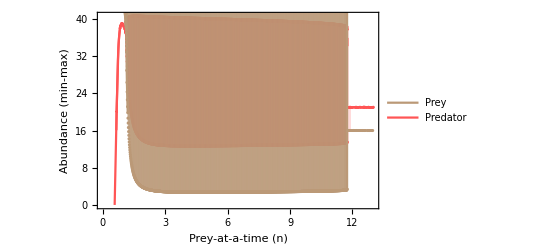

```mathematica
ip={{40,30},{40,10}};
p5=ListPlot[{Flatten[Phighs,1],Flatten[Plows,1]},
Filling->{1->{2}},
ImagePadding->ip,
Joined->False,
PlotRange->{{0,Full},{0,Full}},
PlotStyle->Lighter[Red],
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey-at-a-time (n)",14],Style["Abundance (min-max)",14]}];

p6=ListPlot[{Flatten[PhighsL,1],Flatten[PlowsL,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Red],
PlotRange->{{0,1.2},{0,Full}}];

p7=ListPlot[{Flatten[PhighsH,1],Flatten[PlowsH,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Red],
PlotRange->{{11.6,12},{0,Full}}];

p8=ListPlot[{Flatten[Rhighs,1],Flatten[Rlows,1]},
Filling->{1->{2}},
ImagePadding->ip,
PlotStyle->Lighter[Brown],
PlotRange->{{0,Full},{0,Full}},
Axes->False,Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey-at-a-time (n)",14],Style["Abundance (min-max)",14]}];

p9=ListPlot[{Flatten[RhighsL,1],Flatten[RlowsL,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Brown],
PlotRange->{{0,1.2},{0,Full}}];

p10=ListPlot[{Flatten[RhighsH,1],Flatten[RlowsH,1]},
Filling->{1->{2}},
Joined-> True,
ImagePadding->ip,
PlotStyle->Lighter[Brown],
PlotRange->{{11.6,12},{0,Full}}];

P5=Legended[Show[p5,p6,p7,p8,p9,p10],Placed[LineLegend[{Lighter[Brown],Lighter[Red]},{"Prey","Predator"},
 LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->0.1,
Spacings-> 0.1],
{{0.7,0.76},{0,0}}]]

Export["Bifurcation.pdf",P5,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

## Eigenvalues

Since equilibria can' t be solved for symbolically, proceed numerically.
Note that there are multiple stable feasible (real-valued) solutions at high n (i.e. there is bistability) as seen using Eigs2.

#### Eigenvalues as function of 'n'

```mathematica
MaxRe[λ_]:=Max[Re[λ]];
MaxIm[λ_]:=Max[Im[λ]]; 
(* imaginary parts are always equal magnitude (one positive on negative) so just take max *)
```

```mathematica
Eigs[ν_]:=
Module[{equil,A,Aeq},
equil=Select[NSolve[{dRdt==0,dPdt==0}/.parms/.n-> ν,{R,P}],
Re[#[[1,2]]]>0&&Re[#[[2,2]]]>0 && Im[#[[1,2]]]==0&&Im[#[[2,2]]]==0&]//Flatten;
A=JacobianMatrix[{dRdt,dPdt}/.parms/.n-> ν,{R,P}];
Aeq=A/.equil/.parms/.n-> ν;
Eigenvalues[Aeq]
]
Eigs2[ν_]:=
Module[{equil,A,Aeq,eigs,FeasRP},
equil=Quiet[NSolve[{dRdt==0,dPdt==0}/.parms/.n-> ν,{R,P}]];
FeasRP=Re[R]>0 && Re[P]> 0 && Im[R]==0 && Im[P]==0/.equil;
A=JacobianMatrix[{dRdt,dPdt}/.parms/.n-> ν,{R,P}];
Aeq=A/.Pick[equil,FeasRP];
Map[Eigenvalues,Aeq]]
```

Values at lower n than evaluated are unstable; the predator has gone extinct.

```mathematica
eigs0=Table[{n,Eigs[n]},{n,0.64,0.65,0.01}];
eigs1=Table[{n,Eigs[n]},{n,0.65,0.75,0.05}];
eigs2=Table[{n,Eigs[n]},{n,0.8,1.6,0.2}];
eigs3=Table[{n,Eigs[n]},{n,2,4,0.5}];
eigs4=Table[{n,Eigs[n]},{n,5,13,1}];
eigs=Join[eigs0,eigs1,eigs2,eigs3,eigs4];
```

```mathematica
eigRe=MapAt[MaxRe,eigs,{All,2}];
eigIm=MapAt[MaxIm,eigs,{All,2}];
```

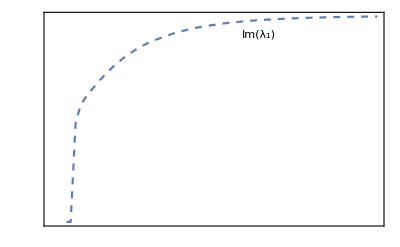
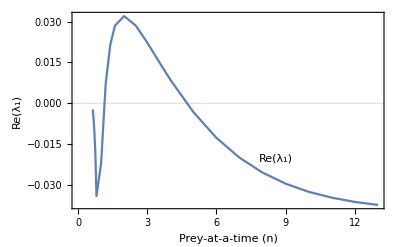

```mathematica
ip={{50,50},{40,10}};
p6=ListPlot[
Callout[eigRe,"Re(λ_1)",{Scaled[0.6],Above},LeaderSize->0,Background->None],
Joined-> True,
ImagePadding->ip,
PlotRangePadding->{{0,0},{0.005,0.01}},
Axes->False,
GridLines->{{-10},{0}},
Frame->{{True,False},{True,False}},
FrameLabel->{Style["Prey-at-a-time (n)",14],
Style["Re(λ_1)",14]}];
p7=ListPlot[
Callout[eigIm,"Im(λ_1)",{Scaled[0.6],Below},LeaderSize->0,Background->None],
Joined-> True,
ImagePadding->ip,
PlotRangePadding->{{0,0},{0,0}},
Axes->True,
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,True}},
PlotStyle-> Dashed,
FrameLabel->
{{None,Style["Im(λ_1)",14]},
{None,None}}];
P6=Overlay[{p7,p6}]

Export["Eigenvalues.pdf",P6,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

#### Eigenvalues as function of ‘n’ and ‘K’

Need to restrict to integer values of  'n' to permit computation in reasonable time

```mathematica
nKparms = Drop[parms,{5}];

StableReImFeasRP[ν_,k_]:=
Module[{equil,A,Aeq,eigs,FeasRP,ReE,ImE},
equil=Quiet[Solve[{dRdt==0,dPdt==0}/.nKparms/.n-> ν/.Κ-> k,{R,P}]];
FeasRP=Re[R]>0 && Re[P]> 0 && Im[R]==0 && Im[P]==0/.equil;
A=JacobianMatrix[{dRdt,dPdt}/.nKparms/.n-> ν/.Κ-> k,{R,P}];
Aeq=A/.Pick[equil,FeasRP];
eigs=Map[Eigenvalues,Aeq];
WhichMaxRe=1; (* Numerical issues (?) at n = 11 cause seeming bistability, so pick only first solution *)
ReE=Map[MaxRe,eigs][[WhichMaxRe]];
ImE=Map[MaxIm,eigs][[WhichMaxRe]];
If[!NumberQ[ReE],out=0,
If[ReE>=0,out=3,
If[ReE<0 && ImE==0,out=1,
If[ReE <0&&ImE>0,out=2]]]];
out
]
```

```mathematica
StableReImFeasRP[11,100]
```

2

```mathematica
nMax=13;
kMin=1;
kMax=250;
kStep=1;
stabReImRP=Table[StableReImFeasRP[n,κ],{κ,kMin,kMax,kStep},{n,1,nMax,1}];
```

$Aborted

```mathematica
xvals = Range[nMax];
yvals=Table[i,{i,0,kMax ,kStep 10}];
xticks=Transpose[{xvals,xvals}];
yticks=Transpose[{Range@Length[yvals] 10-10,yvals}];

P7=ArrayPlot[stabReImRP,
DataReversed->True,
ColorFunctionScaling->False,
ColorFunction->ColorData[{"GrayTones","Reverse"}],
ColorRules->{
x_/;x ==3 -> GrayLevel[0.4],
x_/;x ==2 -> GrayLevel[0.7],
x_/;x ==1 -> GrayLevel[0.9],
x_/;x ==0 -> GrayLevel[0.2]},
PlotRangePadding->None,
Frame->True,
FrameTicks->{{yticks,None},{xticks,None}},
AspectRatio->1,
FrameLabel->{
Style["Prey carrying capacity (K)",14],
Style["Prey-at-a-time (n)",14]},
Epilog->{
Text[Style["Damped oscillations",14],{9,100}],
Text[Style["Monotonic damping",14],{8,23}],
Text[Style["Predator extinction",14, White],{6,8}],
Text[Style["Stable\nlimit cycles",14, White],{3,180}]}]

(* To prevent blurry edges in Preview *)
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],
VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]

Export["Stability_nK.pdf",P7//rasterTrick,"PDF",
"AllowRasterization"->False,ImageSize->360];
```

-Graphics-